```mathematica
raw=Import["/Users/steve/Dropbox/dev/rust/projects/cadusdbtc/log.txt","CSV"];
raw2={#[[1]]
,Interpreter["Number"][
StringReplace[#[[2]],{"{"->"","}"->"","\"CAD\""->"",":"->""}]
]
,Interpreter["Number"][
StringReplace[#[[3]],{"{"->"","}"->"","USD:"->""}]
]
}&/@ raw;
```

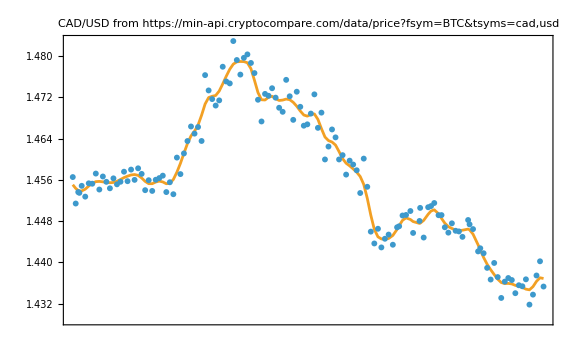

```mathematica
DateListPlot[{
{#[[1]],#[[2]]/#[[3]]}&/@raw2
, GaussianFilter[TimeSeries[{#[[1]],#[[2]]/#[[3]]}&/@raw2],16]
}
,GridLines->Automatic
,Joined->{False,True}
,ImageSize->Large
,ImageMargins->20
,PlotLabel -> Column[{
Style["CAD/USD",{Red,18}]
,"from"
,"https://min-api.cryptocompare.com/data/price?fsym=BTC&tsyms=cad,usd"
}
,Center
]
]
```